# Renormalisation Group Flow of the ϕ^4 QFT

## Rehmat Singh Chawla CID: 06035661 rsc124@ic.ac.uk Mini-Project Submission Module: Research Computing Skills Course: MSc Physics with Extended Research at Imperial College London

### Structure of the Notebook

A Renormalisation Group Flow in the space of theories takes the form of some differential equations involving the energy scale μ and the parameters of the theory m, g, etc. Generally, these equations are described by the β functions:

βg(m,g,...) = μ *dg/dμ

Once these functions are determined, it is straightforward to investigate the flow, its stability conditions, etc. 
This notebook is split into 3 sections:
1. In “Fixed-Point Analysis”, I set up the functionality for plotting the flow and fixed points, given any pair of β functions for a ϕ^4 theory.
2. In “Calculating Behaviour Under Renormalisation”, I use FeynCalc to create and evaluate Feynman diagrams in the ϕ^4 theory. Using the capabilities of FeynCalc, I explicitly calculate the counterterms required for the renormalisation of the ϕ^4 theory at 1-loop order. Then I show how to obtain the β functions from the counterterms.
3. In “Plotting Renormalisation Group Flows”, I plot the flows and their fixed points for the calculated β functions, as well as higher-order β functions available in the literature.

### Settings and Packages

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True];SetOptions[EvaluationNotebook[],CellEpilog:>SelectionMove[EvaluationNotebook[],Next,Cell]];
```

```mathematica
(* If FeynCalc is not installed, run the following and skip the next cell. *)
Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"];
InstallFeynCalc[]
```

```mathematica
(*$LoadAddOns={"FeynArts"};
<<FeynCalc`*)
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

SetDelayed::wrsym: Symbol Discard is Protected.

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
$FAVerbose=1;
FAPatch[PatchModelsOnly->True];
$KeepLogDivergentScalelessIntegrals=True;
```

Successfully patched FeynArts.

```mathematica
(* The phi^4 model must first be generated using FeynRules. I have already generated the model and included it in the ZIP, however the following commands may be used to generate it from scratch. Note that the FeynRules package must be downloaded first, from https://cp3.irmp.ucl.ac.be/projects/feynrules/wiki/WikiStart *)
(*
NotebookEvaluate[FileNameJoin[{$UserBaseDirectory,"Applications/FeynCalc/Examples/FeynRules/Phi4/Mathematica/GenerateModelPhi4.m"}]];
InitializeModel["Phi4/Phi4", GenericModel ->"Phi4/Phi4"];
*)
modelLocation = FileNameJoin[NotebookDirectory[],"Phi4/Phi4"];
InitializeModel[modelLocation, GenericModel ->modelLocation];
```

generic model {/Users/r/Documents/Imperial/Sem 1/RCS/Mini-Project/Final Submission/Phi4/Phi4} initialized

classes model {/Users/r/Documents/Imperial/Sem 1/RCS/Mini-Project/Final Submission/Phi4/Phi4} initialized

## Fixed-Point Analysis

For example, consider the 1st order β functions for ϕ^4 [1]. Note that m2 refers to m^2, the coefficient of the quadratic interaction, which is generally allowed to be negative.

```mathematica
βm2[m2_,g_,ε_]:= m2*g
βg[m2_,g_,ε_]:= 3*g^2-g*ε
```

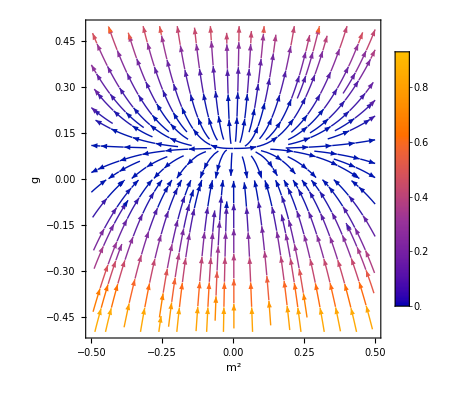

```mathematica
mRange = 0.5;
gRange = mRange;
ε0 = 0.3;
RGFlow = StreamPlot[{βm2[m2,g,ε0],βg[m2,g,ε0]},{m2,-mRange,mRange},{g,-gRange,gRange},PlotLegends->Automatic,FrameLabel->{m^2,g}]
```

We have the flow. We can also analyse the stability conditions of this flow. βg can also be understood as the derivative of g with respect to Log[μ], referred to as ν.

```mathematica
DStabilityConditions[{m2'[ν]==βm2[m2[ν],g[ν],ε],g'[ν]==βg[m2[ν],g[ν],ε]},{m2[ν],g[ν]},ν,Assumptions->ε>=0]
```

({0,ε/3} | ε≤0
{K[1],0} | True)

The second column indicates if the fixed point/region is stable. K[1] is a constant of integration. This means the line g=0 is a stable fixed region, whereas the point (0,ε/3) is unstable for ε > 0 .
If we want to plot this, it is easier to do so using regions:

```mathematica
fixedPointConditions[ε_] = Solve[{0==βm2[m2,g,ε],0==βg[m2,g,ε]},{m2,g}]/. Rule-> Equal
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{g==0},{m2==0,g==ε/3}}

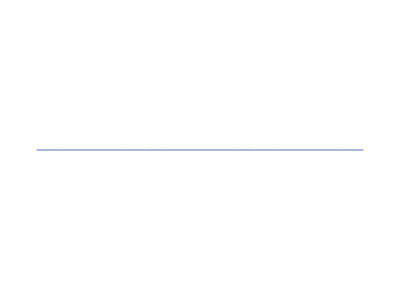
{-Graphics-,Region[…]}

```mathematica
fixedRegions[ε_] = Region[ImplicitRegion[#,{m2,g}]]&/@ fixedPointConditions[ε]
```

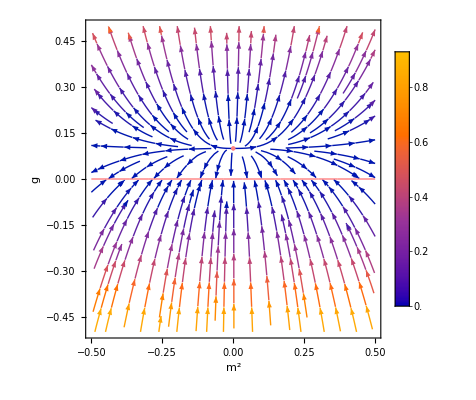

```mathematica
fixedRegionPlots = Region[Style[#, Pink, PointSize[Large],Thick],PlotRange->{{-mRange,mRange},{-gRange,gRange}}]&/@fixedRegions[ε0];
Show[RGFlow,fixedRegionPlots]
```

Compile all this into a single function:

```mathematica
flowAndFixedRegionPlots[βm2_,βg_,ε0_,mRange_,gRange_] := Module[{RGFlow,fixedPointConditions,fixedRegions,fixedRegionPlots,mMin,mMax,gMin,gMax},
gMin=-gRange;gMax=gRange;
If[gRange[[0]]==List,gMin=gRange[[1]];gMax=gRange[[2]]]; 
mMin=-mRange;mMax=mRange;
If[mRange[[0]]==List,mMin=mRange[[1]];mMax=mRange[[2]]]; 
RGFlow = StreamPlot[{βm2[m2,g,ε0],βg[m2,g,ε0]},{m2,mMin,mMax},{g,gMin,gMax},PlotLegends->Automatic,FrameLabel->{m^2,g}];
DStabilityConditions[{m2'[ν]==βm2[m2[ν],g[ν],ε],g'[ν]==βg[m2[ν],g[ν],ε]},{m2[ν],g[ν]},ν,Assumptions->ε>=0]//Print;
fixedPointConditions[ϵ_] = Solve[{0==βm2[m2,g,ϵ],0==βg[m2,g,ϵ]},{m2,g}]/. Rule-> Equal;
fixedRegions[ϵ_] = Region[ImplicitRegion[#,{m2,g}]]&/@ fixedPointConditions[ϵ];
fixedRegionPlots = Region[Style[#, Pink, PointSize[Large],Thick],PlotRange->{{mMin,mMax},{gMin,gMax}}]&/@fixedRegions[ε0];
Show[RGFlow,fixedRegionPlots]
]
```

({0,ε/3} | ε≤0
{K[1],0} | True)

Solve::svars: Equations may not give solutions for all "solve" variables.

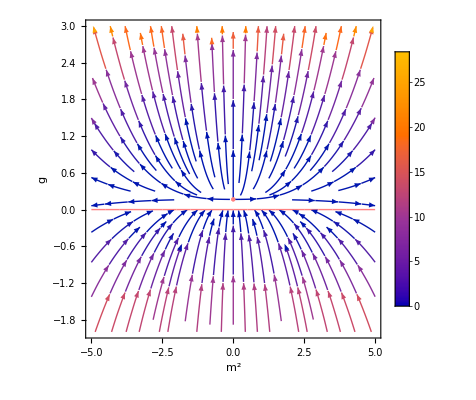

```mathematica
flowAndFixedRegionPlots[βm2,βg,0.5,5,{-2,3}]
```

## Calculating Behaviour Under Renormalisation

### Feynman Diagrams for corrections to Self-Energy and 4-Particle interaction

```mathematica
nLoopOrder = 1;
parameters = {InsertionLevel->{Particles}, Model->modelLocation, GenericModel -> modelLocation};
selfEnergyDiagrams[nLoopOrder] = InsertFields[CreateTopologies[nLoopOrder,1-> 1],{S[1]}->{S[1]}, Sequence @@ parameters];
selfEnergyCountertermDiagrams[nLoopOrder] = InsertFields[CreateCTTopologies[nLoopOrder,1-> 1],{S[1]}->{S[1]},Sequence @@ parameters];
vertexDiagrams[nLoopOrder] = InsertFields[CreateTopologies[nLoopOrder,2-> 2,ExcludeTopologies->{WFCorrections}],
										{S[1],S[1]}->{S[1],S[1]},Sequence @@ parameters];
vertexCountertermDiagrams[nLoopOrder] = InsertFields[CreateCTTopologies[nLoopOrder,2-> 2,ExcludeTopologies->{WFCorrectionCTs}],
										{S[1],S[1]}->{S[1],S[1]},Sequence @@ parameters];
```

in total: 1 Particles insertion

in total: 1 Particles insertion

in total: 3 Particles insertions

in total: 1 Particles insertion

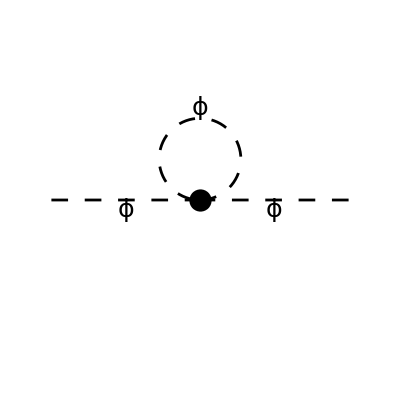

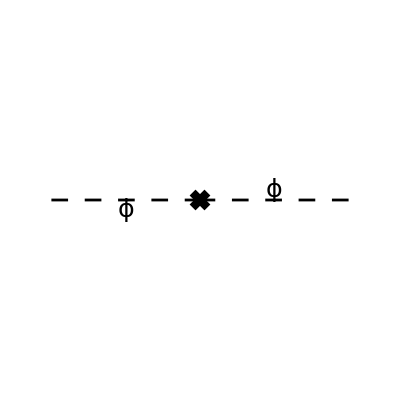

```mathematica
(* Self-energy diagrams and counterterms at 1-loop order *)
Paint[selfEnergyDiagrams[nLoopOrder],ColumnsXRows->{1,1},Numbering->None];
Paint[selfEnergyCountertermDiagrams[nLoopOrder],ColumnsXRows->{1,1},Numbering->None];
```

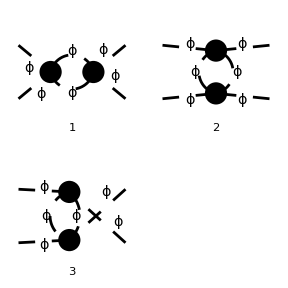

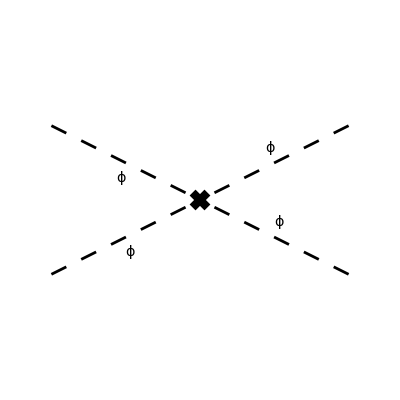

```mathematica
(* 4-point vertex diagrams and counterterms at 1-loop order *)
Paint[vertexDiagrams[nLoopOrder],ColumnsXRows->{2,2},Numbering->Simple];
Paint[vertexCountertermDiagrams[nLoopOrder],ColumnsXRows->{1,2},Numbering->None];
```

### Self-Energy Calculations

```mathematica
selfEnergyCorrections[nLoopOrder] =
FCFAConvert[CreateFeynAmp[selfEnergyDiagrams[nLoopOrder],PreFactor->1],
			IncomingMomenta->{p},OutgoingMomenta->{p},LorentzIndexNames->{mu},LoopMomenta->{k},
			ChangeDimension->D,List->False,SMP->True,
			FinalSubstitutions->{Zm->SMP["Z_m"],Zphi->SMP["Z_phi"],Mphi->m}
			] +
FCFAConvert[CreateFeynAmp[selfEnergyCountertermDiagrams[nLoopOrder],PreFactor->1],
			IncomingMomenta->{p},OutgoingMomenta->{p},LorentzIndexNames->{mu},LoopMomenta->{k},
			ChangeDimension->D,List->False,SMP->True,
			FinalSubstitutions->{Zm->SMP["Z_m"],Zphi->SMP["Z_phi"],Mphi->m}
			]
```

in total: 1 Particles amplitude

in total: 1 Particles amplitude

g/(2 (k^2-m^2))-ⅈ m^2 (Z_m Z_ϕ-1)+ⅈ p^2 (Z_ϕ-1)

```mathematica
(* The counterterms Z can be expanded in terms of some small α. *)
selfEnergyCorrections[nLoopOrder] = selfEnergyCorrections[nLoopOrder]/.{SMP["Z_phi"]->1+α SMP["d_phi"],SMP["Z_m"]->1+α SMP["d_m"]}//Series[#,{α,0,1}]& //Normal //ReplaceAll[#,α-> 1]&
```

g/(2 (k^2-m^2))-ⅈ m^2 (δ_ϕ+δ_m)+ⅈ p^2 δ_ϕ

```mathematica
(* The internal momenta k must be integrated over, but this leads to a divergence. We account for this by replacing them with the Passarino-Veltman coefficient functions. We can then analytically continue to non-integral dimensions D-ε and discard the divergent behaviour. *)
selfEnergyCorrections[nLoopOrder] = selfEnergyCorrections[nLoopOrder] // ToPaVe[#,k]& // PaVeUVPart[#,Prefactor->1/(2 Pi)^D] & //FCReplaceD[#,D->4- Epsilon]& //Series[#,{Epsilon,0,1}]&//Normal  //FCHideEpsilon//SelectNotFree2[#,{SMP["Delta"],SMP["d_m"],SMP["d_phi"]}]& //Simplify
```

(ⅈ Δ g m^2)/(16 π^2)-ⅈ (m^2 δ_m+δ_ϕ (m^2-p^2))

```mathematica
δPhiSolution=Solve[SelectNotFree2[selfEnergyCorrections[nLoopOrder],p]==0,SMP["d_phi"]]/. {SMP["Delta"]->1/Epsilon}//Flatten; 
δmSolution=Solve[(SelectFree2[selfEnergyCorrections[nLoopOrder],p]==0)/. δPhiSolution,SMP["d_m"]]/. {SMP["Delta"]->1/Epsilon}//Flatten;
δSolutions=Join[δPhiSolution,δmSolution]
```

{δ_ϕ→0,δ_m→g/(16 π^2 ε)}

```mathematica
(* With these, we can re-obtain the counterterms, and from them, the β functions *)
Zphi[μ_] = 1+SMP["d_phi"]/.δPhiSolution/.{m-> Sqrt[m2[μ]],g->g[μ],Epsilon->ε}
Zm2[μ_] = 1+ SMP["d_m"]/.δmSolution/.{m-> Sqrt[m2[μ]],g->g[μ],Epsilon->ε}
```

1

(g(μ))/(16 π^2 ε)+1

### 4-Point Vertex Calculations

```mathematica
vertexCorrections[nLoopOrder] =FCFAConvert[CreateFeynAmp[vertexDiagrams[nLoopOrder],PreFactor->1],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LorentzIndexNames->{mu},LoopMomenta->{k},ChangeDimension->D,List->False,SMP->True,FinalSubstitutions->{Zg->SMP["Z_g"],Zphi->SMP["Z_phi"],Mphi->m}] +
FCFAConvert[CreateFeynAmp[vertexCountertermDiagrams[nLoopOrder],PreFactor->1],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LorentzIndexNames->{mu},LoopMomenta->{k},ChangeDimension->D,List->False,SMP->True,FinalSubstitutions->{Zg->SMP["Z_g"],Zphi->SMP["Z_phi"],Mphi->m}]
```

in total: 3 Particles amplitudes

in total: 1 Particles amplitude

g^2/(2 (k^2-m^2).((k+p2-p3)^2-m^2))+g^2/(2 (k^2-m^2).((k+p2-p4)^2-m^2))+g^2/(2 (k^2-m^2).((k-p3-p4)^2-m^2))-ⅈ g (Z_g Z_ϕ^2-1)

```mathematica
(* The counterterms Z can be expanded in terms of some small α. *)
vertexCorrections[nLoopOrder] = vertexCorrections[nLoopOrder]/.{SMP["Z_g"]->1+α SMP["d_g"],SMP["Z_phi"]->1+α SMP["d_phi"]}//Series[#,{α,0,1}]& //Normal //ReplaceAll[#,α-> 1]&
```

1/2 (g^2/((k^2-m^2).((k+p2-p3)^2-m^2))+g^2/((k^2-m^2).((k+p2-p4)^2-m^2))+g^2/((k^2-m^2).((k-p3-p4)^2-m^2)))-ⅈ g (2 δ_ϕ+δ_g)

```mathematica
(* The internal momenta k must be integrated over, but this leads to a divergence. We account for this by replacing them with the Passarino-Veltman coefficient functions. We can then analytically continue to non-integral dimensions D-ε and discard the divergent behaviour. *)
vertexCorrections[nLoopOrder] = vertexCorrections[nLoopOrder]// ToPaVe[#,k]& // PaVeUVPart[#,Prefactor->1/(2 Pi)^D] & //FCReplaceD[#,D->4- Epsilon]& //Series[#,{Epsilon,0,1}]&//Normal  //FCHideEpsilon//SelectNotFree2[#,{SMP["Delta"],SMP["d_g"],SMP["d_phi"]}]& //Simplify
```

1/16 ⅈ g ((3 Δ g)/π^2-16 (2 δ_ϕ+δ_g))

```mathematica
δgSolution=Solve[vertexCorrections[nLoopOrder]==0/.δPhiSolution,SMP["d_g"]]/. {SMP["Delta"]->1/Epsilon}//Flatten
```

{δ_g→(3 g)/(16 π^2 ε)}

```mathematica
Zg[μ_] = 1+SMP["d_g"]/.δgSolution/.{m-> Sqrt[m2[μ]],g->g[μ],Epsilon->ε}
```

(3 g(μ))/(16 π^2 ε)+1

### Obtaining β Functions

```mathematica
mExpr = Log[m2[μ]] +Log[Zm2[μ]/ Zphi[μ]];
gExpr = Log[g[μ]] + Log[ Zg[μ]/Zphi[μ]^2*μ^ε];
renormalisedEquations =({Zm2[μ]*D[mExpr,μ] ==0, Zg[μ]*D[gExpr,μ] ==0}/. {g'[μ]-> (-ε*g[μ]+γ)/μ,m2'[μ]->βm2/μ}//Simplify//Expand)/.{1/ε->0}
```

{(16 π^2 βm2)/(μ m2(μ))-(g(μ))/μ==0,(16 π^2 γ)/(μ g(μ))-(3 g(μ))/μ==0}

```mathematica
betaFunctions = Solve[renormalisedEquations,{βm2,γ}]
```

{{βm2→(g(μ) m2(μ))/(16 π^2),γ→(3 (g(μ))^2)/(16 π^2)}}

```mathematica
βmCalculated[m2_,g_,ε_]=( βm2/.betaFunctions [[1]] )/.{m2(μ)->m2, g(μ)-> g}
βgCalculated[m2_,g_,ε_]=( -ε*g[μ]+γ/.betaFunctions [[1]]  )/.{m2(μ)->m2, g(μ)-> g}
```

(g m2)/(16 π^2)

(3 g^2)/(16 π^2)-ε g

## Plotting Renormalisation Group Flows

({0,(16 π^2 ε)/3} | ε≤0
{K[1],0} | True)

Solve::svars: Equations may not give solutions for all "solve" variables.

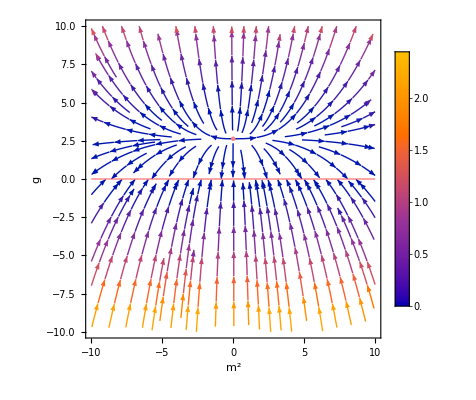

```mathematica
flowAndFixedRegionPlots[βmCalculated,βgCalculated,0.05,10,10]
```

We can also examine how the flow changes with a varying ε:

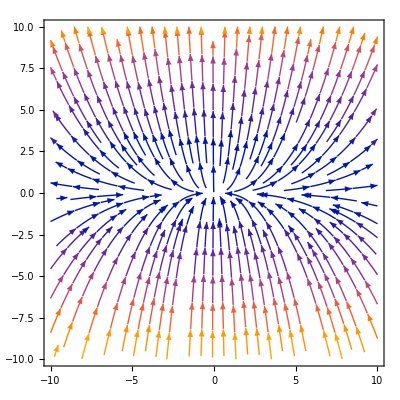
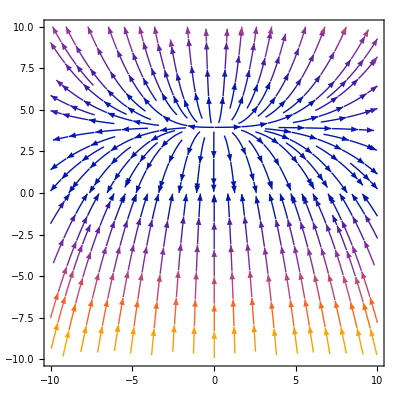
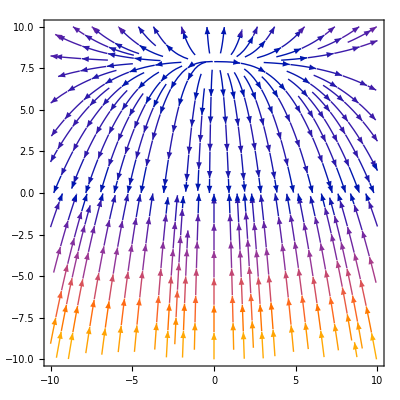

```mathematica
Table[StreamPlot[{βmCalculated[m2,g,i*3/40],βgCalculated[m2,g,i*3/40]},{m2,-10,10},{g,-10,10}],{i,0,2}]
```

### Higher-Order β Functions

β functions obtained using higher-order corrections can be found in the literature [2]. Let us see how the flow differs for these:

```mathematica
βgHigherLoop[m2_,g_,ε_]=(−ε*g+3g^2−5.667g^3+32.55g^4−271.6g^5+2849g^6−34776g^7)/(2Pi)^2
βmHigherLoop[m2_,g_,ε_]=-m2*(−g+0.8333g^2−3.5g^3+19.96g^4−150.8g^5+1355g^6)/(2Pi)^2
```

(-34776 g^7+2849 g^6-271.6 g^5+32.55 g^4-5.667 g^3+3 g^2-ε g)/(4 π^2)

-((1355 g^6-150.8 g^5+19.96 g^4-3.5 g^3+0.8333 g^2-g) m2)/(4 π^2)

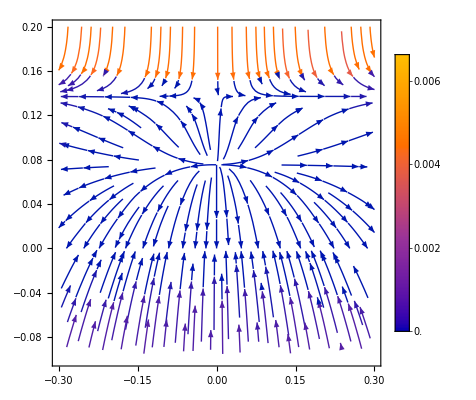

```mathematica
mRange = 0.3;
gMax = 0.2;
gMin = -0.1;
ε0= 0.2;
StreamPlot[{βmHigherLoop[m,g,ε0],βgHigherLoop[m,g,ε0]},{m,-mRange,mRange},{g,gMin,gMax},PlotLegends->Automatic]
```

```mathematica
fixedPoints = DStabilityConditions[{mSquare'[mu]==βmHigherLoop[mSquare[mu],g[mu],ε0],g'[mu]==βgHigherLoop[mSquare[mu],g[mu],ε0]},{mSquare[mu],g[mu]},mu,Assumptions->ε>=0]
```

({0,0} | True
{0,0.0755329} | False
{0,0.137048} | False
{K[1],ConditionalExpression[0, K[1]≠0]} | True)

## Bibliography

```mathematica
FeynCalcHowToCite[]
```

• V. Shtabovenko, R. Mertig and F. Orellana, arXiv:2312.14089.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts: 
• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260
[1] : Zinn-Justin, Jean. 2002. Quantum Field Theory and Critical Phenomena. 4th ed. Oxford, New York: Clarendon Press.
[2] : Kompaniets, Mikhail, and Erik Panzer. 2016. ‘Renormalization Group Functions of $φ^4$ Theory in the MS-Scheme to Six Loops’. arXiv. https://doi.org/10.48550/arXiv.1606.09210.